```mathematica
w=-1;
Subscript[Ω, DE0]=0.734;
Subscript[Ω, k0]=0;
Subscript[Ω, m0]=0.1334/(0.71^2)
Subscript[Ω, r0]=8.09*10^-5
1/(a^2 √(a^(-3-3 w) Subscript[Ω, DE0]+Subscript[Ω, k0]/a^2+Subscript[Ω, m0]/a^3+Subscript[Ω, r0]/a^4))
```

0.26463

0.0000809

1/(√(0.734+0.0000809/a^4+0.26463/a^3) a^2)

Test:

```mathematica
NIntegrate[1/(√(0.734 a^4+8.09 *10^-5+0.26463 a)),{a,0,10^-3}]
```

0.0725087

## Plot the Hubble distance of scale factor a

Use NIntegrate, for Integrate gives complex numbers when a is small.

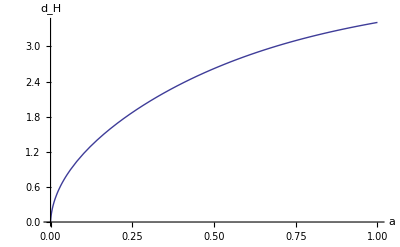

```mathematica
Plot[NIntegrate[1/(√(0.734 a^4+8.09 *10^-5+0.26463 a)),{a,0,y}],{y,0,1},AxesLabel-> {a,Subscript[d, H]}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in a near {a} = {-0.721646}. NIntegrate obtained -2.43123 + 4.02693\ ⅈ and 0.412471 for the integral and error estimates.

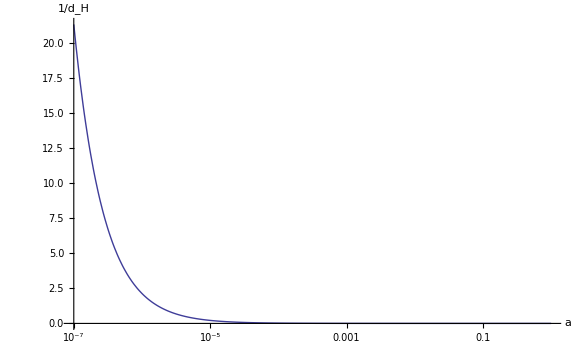

```mathematica
LogLinearPlot[(71/300000)/NIntegrate[1/(√(0.734 a^4+8.09 *10^-5+0.26463 a)),{a,0,y}],{y,10^-7,1},AxesLabel-> {a,1/Subscript[d, H]},AxesOrigin-> {10^-7,0},PlotRange->Full,WorkingPrecision->MachinePrecision]
```

## Growth function

```mathematica
w=-1;
Subscript[Ω, DE0]=0.734;
Subscript[Ω, k0]=0;
Subscript[Ω, m0]=0.1334/(0.71^2);
Subscript[Ω, r0]=8.09*10^-5;
SubPlus[D] [a] = 5/2 Subscript[Ω, m0] a^-3  √(a^(-3-3 w) Subscript[Ω, DE0]+Subscript[Ω, k0]/a^2+Subscript[Ω, m0]/a^3+Subscript[Ω, r0]/a^4)  Integrate[1/((m ( m^(-3-3 w) Subscript[Ω, DE0]+Subscript[Ω, k0]/m^2+Subscript[Ω, m0]/m^3+Subscript[Ω, r0]/m^4)^0.5)^3),{m,0,a}]
```

(0.661575 √(0.734+0.0000809/a^4+0.26463/a^3) ∫_0^a 1/((0.734+0.0000809/m^4+0.26463/m^3)^1.5 m^3)ⅆm)/a^3

```mathematica
w=-1;
Subscript[Ω, DE0]=0.734;
Subscript[Ω, k0]=0;
Subscript[Ω, m0]=0.1334/(0.71^2);
Subscript[Ω, r0]=8.09*10^-5;
1/((m ( m^(-3-3 w) Subscript[Ω, DE0]+Subscript[Ω, k0]/m^2+Subscript[Ω, m0]/m^3+Subscript[Ω, r0]/m^4)^0.5)^3)
```

1/((0.734+0.0000809/m^4+0.26463/m^3)^1.5 m^3)

Start Plotting

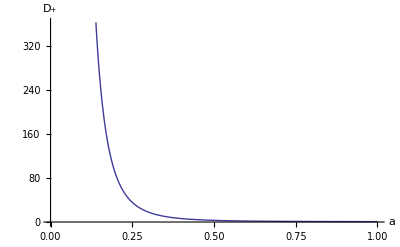

```mathematica
w=-1;
Subscript[Ω, DE0]=0.734;
Subscript[Ω, k0]=0;
Subscript[Ω, m0]=0.1334/(0.71^2);
Subscript[Ω, r0]=8.09*10^-5;
Plot[0.6615750843086688 √(0.734+0.0000809/a^4+0.26463003372346755/a^3) NIntegrate[1/((0.734+0.0000809/m^4+0.26463003372346755/m^3)^1.5 m^3),{m,0,1}]/NIntegrate[1/((0.734+0.0000809/m^4+0.26463003372346755/m^3)^1.5 m^3),{m,0,a}],{a,0,1},AxesLabel-> {a,SubPlus[D]}]
```

## Combination of Growth Function & Hubble Distance

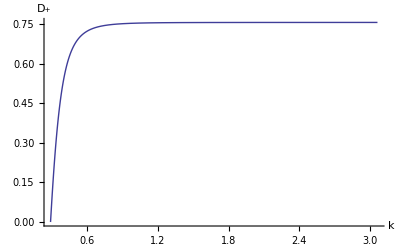

-12.0539+105.684 x-383.169 x^2+794.032 x^3-1030.73 x^4+866.088 x^5-469.909 x^6+158.423 x^7-30.0532 x^8+2.43829 x^9

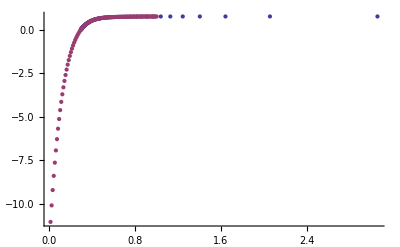

```mathematica
k[a_]:=1/NIntegrate[1/(√(0.734 x^4+8.09 *10^-5+0.26463 x)),{x,0,a}];
Grow[a_] :=0.6615750843086688 NIntegrate[1/((0.734+0.0000809/m^4+0.26463003372346755/m^3)^1.5 m^3),{m,a,1}];
ParametricPlot[{k[a],Growth[a]},{a,0.01,1}];
Table[{k[a],Grow[a]},{a,0.01,1,0.01}];
ListPlot[Table[{k[a],Grow[a]},{a,0.01,1,0.01}],Joined->True, AxesLabel-> {k,SubPlus[D]},AxesOrigin -> {0,0.2},PlotRange->Automatic]
GrowfitLCDM[x_]=Fit[Table[{k[a],Grow[a]},{a,0.01,1,0.01}], {1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9},x]
ListPlot[{Table[{k[x],Grow[x]},{x,0.01,1,0.01}],Table[{x,GrowfitLCDM[x]},{x,0.01,1,0.01}]}]
```

The last figure shows the fitting is good. Next use this fitting function to calculate Q.

## Growth vs k in sCDM

```mathematica
w=-1;
Subscript[Ω, DE0]=0;
Subscript[Ω, k0]=0;
Subscript[Ω, r0]=8.09*10^-5;
Subscript[Ω, m0]=1-Subscript[Ω, r0];
1/(a^2 √(a^(-3-3 w) Subscript[Ω, DE0]+Subscript[Ω, k0]/a^2+Subscript[Ω, m0]/a^3+Subscript[Ω, r0]/a^4))
```

1/(√(0.0000809/a^4+0.999919/a^3) a^2)

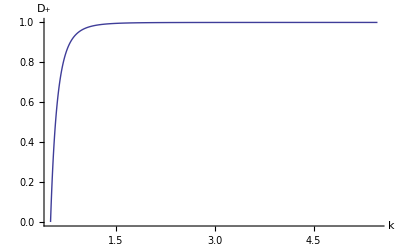

-28.6661+160.67 x-374.427 x^2+488.968 x^3-392.735 x^4+200.809 x^5-65.3132 x^6+13.0269 x^7-1.44536 x^8+0.0679209 x^9

0.954909

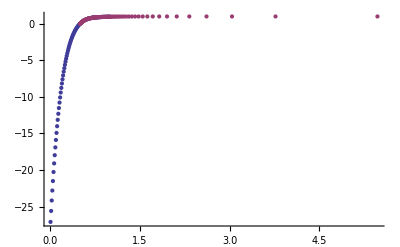

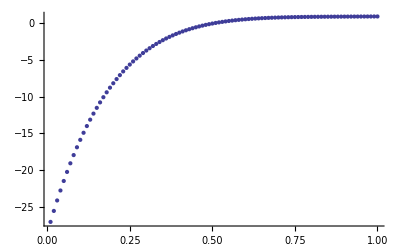

```mathematica
k[a_]:=1/NIntegrate[1/(√(0.0000809+0.9999191 x)),{x,0,a}];
Grow[a_] := 2.5NIntegrate[1/((0.0000809/m^4+0.9999191/m^3)^1.5 m^3),{m,a,1}];
ListPlot[Table[{k[a],Grow[a]},{a,0.01,1,0.01}],Joined->True, AxesLabel-> {k,SubPlus[D]},AxesOrigin -> {0,0.2}]
GrowfitsCDM[x_]=Fit[Table[{k[a],Grow[a]},{a,0.01,1,0.01}], {1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9},x]
GrowfitsCDM[1]
ListPlot[{Table[{x,GrowfitsCDM[x]},{x,0.01,1,0.01}],Table[{k[x],Grow[x]},{x,0.01,1,0.01}]}]
ListPlot[Table[{x,GrowfitsCDM[x]},{x,0.01,1,0.01}]]
```

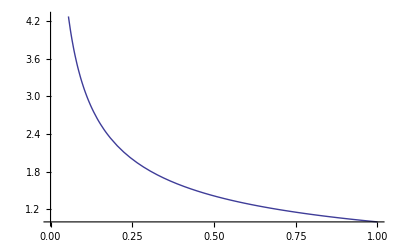

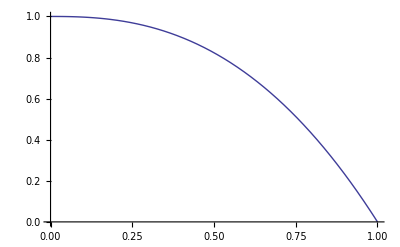

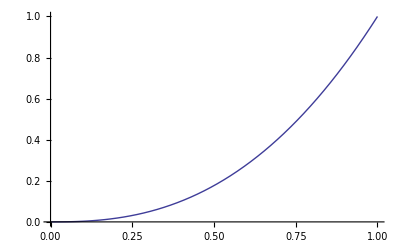

```mathematica
Plot[1/NIntegrate[1/(√(0.0000809/a^4+0.9999191/a^3) a^2),{x,0,a}],{a,0,1}]
Plot[2.5NIntegrate[1/((0.0000809/m^4+0.9999191/m^3)^1.5 m^3),{m,a,1}],{a,0,1}]
Plot[2.5NIntegrate[1/((0.0000809/m^4+0.9999191/m^3)^1.5 m^3),{m,0,a}],{a,0,1}]
```

## Ratio

(-0.0000725343+0.000286358 k-0.000481748 k^2+0.000454784 k^3-0.000267113 k^4+1.0001 k^5-0.000025907 k^6+4.3188×10^-6 k^7-4.59147×10^-7 k^8-3.68231×10^-9 k^9)/(-12.0539+105.684 k-383.169 k^2+794.032 k^3-1030.73 k^4+866.088 k^5-469.909 k^6+158.423 k^7-30.0532 k^8+2.43829 k^9)

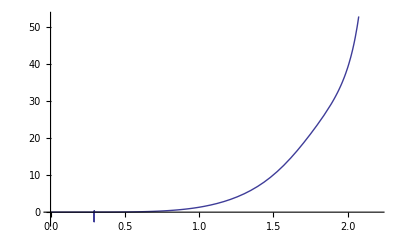

```mathematica
GrowfitsCDM[k_]=-0.00007253427448917655+0.00028635793435248877 k-0.00048174780313690554 k^2+0.00045478432498619525 k^3-0.0002671127589179613 k^4+1.000102257485859 k^5-0.00002590695166325293 k^6+4.3187984208677825*^-6 k^7-4.591473997110464*^-7 k^8-3.682314974455195*^-9 k^9;
GrowfitLCDM[k_]=-12.0538862887343+105.68404141373027 k-383.1689665914246 k^2+794.031884967925 k^3-1030.7268403719222 k^4+866.0883521118186 k^5-469.9090929166467 k^6+158.4229196002385 k^7-30.053233449545008 k^8+2.4382866916404846 k^9;
Q[k_]=GrowfitsCDM[k]/GrowfitLCDM[k]
Plot[Q[k],{k,0,2.2}]
```

## Draft

Power::infy: Infinite expression 1/0. encountered.

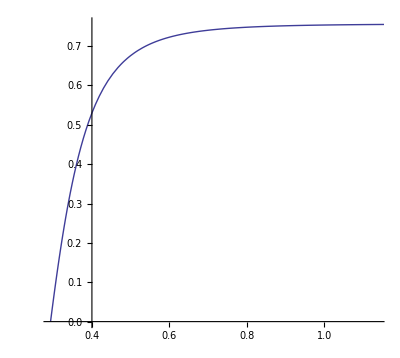

```mathematica
ParametricPlot[{1/NIntegrate[1/(√(0.734 x^4+8.09 *10^-5+0.26463 x)),{x,0,a}], 0.6615750843086688 NIntegrate[1/((0.734+0.0000809/m^4+0.26463003372346755/m^3)^1.5 m^3),{m,a,1}]},{a,0,1}]
```

```mathematica
k_LCDM[a_]=1/NIntegrate[1/√(0.734 x^4+8.09 *10^-5+0.26463 x)  ,{x,0,a}];
Grow_LCDM[a_] = 1/ 0.6615750843086688 NIntegrate[1/((0.734+0.0000809/m^4+0.26463003372346755/m^3)^1.5 m^3),{m,0,a}] 0.6615750843086688 NIntegrate[1/((0.734+0.0000809/m^4+0.26463003372346755/m^3)^1.5 m^3),{m,0,1}];
ParametricPlot[{Grow_LCDM[a],k}]
```

-12.0539+105.684 x-383.169 x^2+794.032 x^3-1030.73 x^4+866.088 x^5-469.909 x^6+158.423 x^7-30.0532 x^8+2.43829 x^9

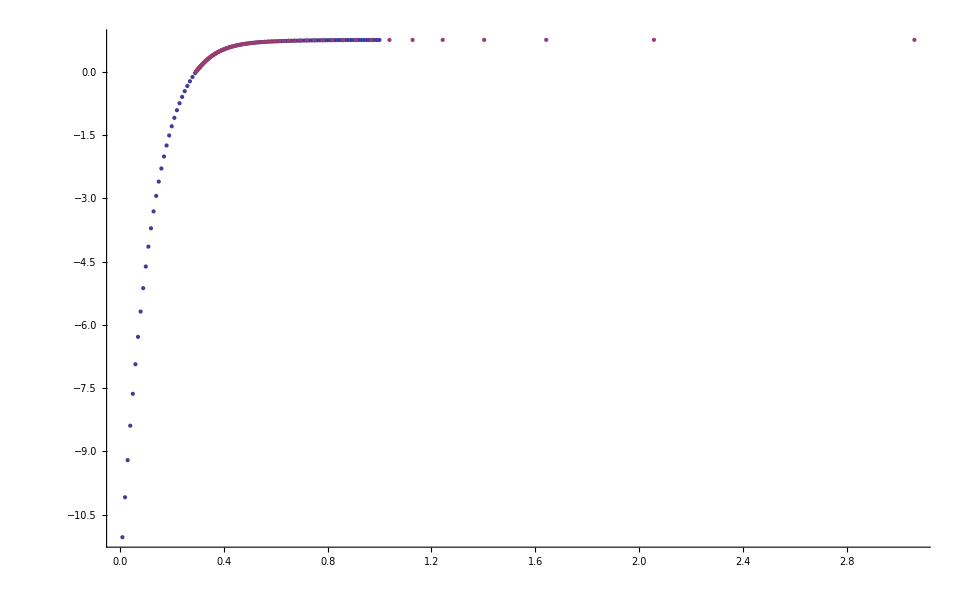

```mathematica
k[a_]:=1/NIntegrate[1/√(0.734 x^4+8.09 *10^-5+0.26463 x)  ,{x,0,a}];
Grow[b_] := 0.6615750843086688 NIntegrate[1/((0.734+0.0000809/m^4+0.26463003372346755/m^3)^1.5 m^3),{m,b,1}];
xyz[x_]=Fit[Table[{k[a],Grow[a]},{a,0.01,1,0.01}], {1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9},x]
ListPlot[{Table[{x,xyz[x]},{x,0.01,1,0.01}],Table[{k[x],Grow[x]},{x,0.01,1,0.01}]}]
```

```mathematica
Table[]
ListPlot[-0.00007253427448917655+0.00028635793435248877 x-0.00048174780313690554 x^2+0.00045478432498619525 x^3-0.0002671127589179613 x^4+1.000102257485859 x^5-0.00002590695166325293 x^6+4.3187984208677825*^-6 x^7-4.591473997110464*^-7 x^8-3.682314974455195*^-9 x^9,{x,0,1}]
```

ListPlot::nonopt: Options expected (instead of {x, 0, 1}) beyond position 1 in ListPlot[-0.0000725343 + 0.000286358\ x - 0.000481748\ x^2 + 0.000454784\ x^3 - 0.000267113\ x^4 + 1.0001\ x^5 - 0.000025907\ x^6 + 4.3188×10^-6\ x^7 - 4.59147×10^-7\ x^8 - 3.68231×10^-9\ x^9, {x, 0, 1}]. An option must be a rule or a list of rules.

ListPlot[-0.0000725343+0.000286358 x-0.000481748 x^2+0.000454784 x^3-0.000267113 x^4+1.0001 x^5-0.000025907 x^6+4.3188×10^-6 x^7-4.59147×10^-7 x^8-3.68231×10^-9 x^9,{x,0,1}]

## aaaa

```mathematica
(*********************************************)
Print[Style["Parameters",Orange]]
(*********************************************)
Subscript[w, 1]=-1;
Subscript[w, 2]=-0.25;
Subscript[w, 3]=-0.5;
Subscript[w, 4]=-0.75;
Subscript[d, 0]=0.734;
Subscript[Ω, k0]=0;
Subscript[m, 0]=0.1334/(0.71^2);
Subscript[r, 0]=8.09*10^-5;
h=0.71;
Subscript[H, 0]=(100 h)/300000
(*********************************************)
Print[Style["Intial conditions for Hubble constant, normalized at equality",Orange]]
(*********************************************)
Subscript[H, s][a_]:=z √(m a^-3+r a^-4)
Subscript[H, L][a_]:=Subscript[H, 0]  √(Subscript[m, 0] a^-3+Subscript[r, 0] a^-4+Subscript[d, 0])
Subscript[H, L][1]
Subscript[H, L][10^-6]
Subscript[H, L][0.333]
Subscript[H, s][1]==1.25 Subscript[H, L][1]
Subscript[H, s][10^-6]==Subscript[H, L][10^-6]
Subscript[H, s][0.333]==1.9 Subscript[H, L][0.333]
Solve[{Subscript[H, s][1]==1.25 Subscript[H, L][1],Subscript[H, s][10^-6]==Subscript[H, L][10^-6],Subscript[H, s][0.333]==1.9 Subscript[H, L][0.333]},{m,r,z}]
Solve[{1.*^9 √(m+1000000 r) z==2.132163481328557*^6,√(m+r) z==0.0002956425974589786,√(27.081162270405564 m+81.32481162283952 r) z==0.0012644406038756924},{m,r,z}]
Eliminate[{√(27.081162270405564 m+81.32481162283952 r) z==0.0012644406038756924,√(m+r) z==0.0002956425974589786},z]
```

Parameters

0.000236667

Intial conditions for Hubble constant, normalized at equality

0.000236514

2.13216×10^6

0.000665495

√(m+r) z==0.000295643

√(1000000000000000000 m+1000000000000000000000000 r) z==2.13216×10^6

√(27.0812 m+81.3248 r) z==0.00126444

{}

{}

-8.72319×10^48 r==1.21633×10^48 m

Parameters

Intial conditions for Hubble constant, normalized at equality

0.00030571

0.000295833

0.000236288

0.000236666

0.000236667

Define Hubble functions

Hubble distances

Define k of a

Define growth factors

Plot k of a

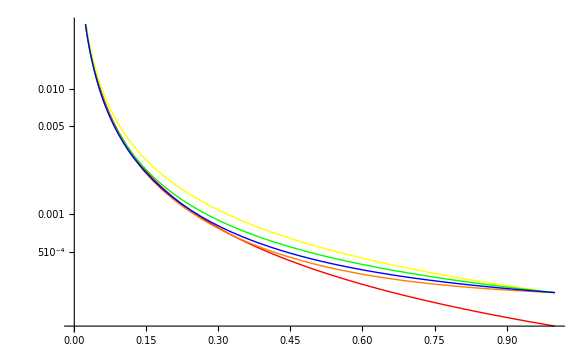

Plot growth factors of a for LCDM

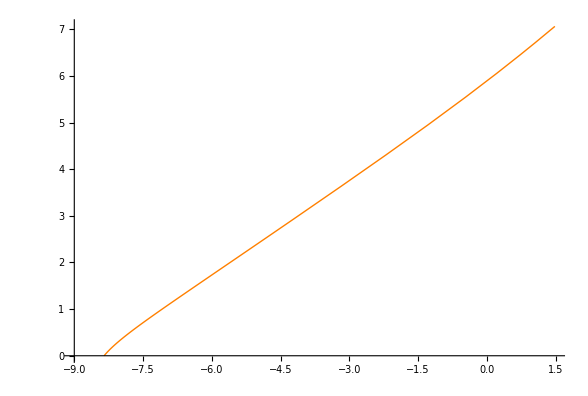

Plot growth factors of a for all models

NIntegrate::nlim: x = a is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.7194}. NIntegrate obtained 41.459  + 55.5417\ ⅈ
 and 38.5744 for the integral and error estimates.

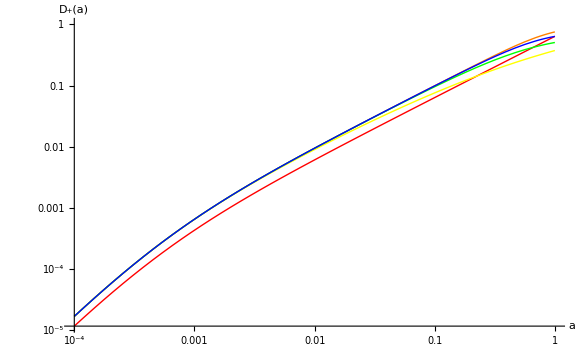

Tranform growth factors / Hubble distances of a to those of 1+z

Plot Hubble distances

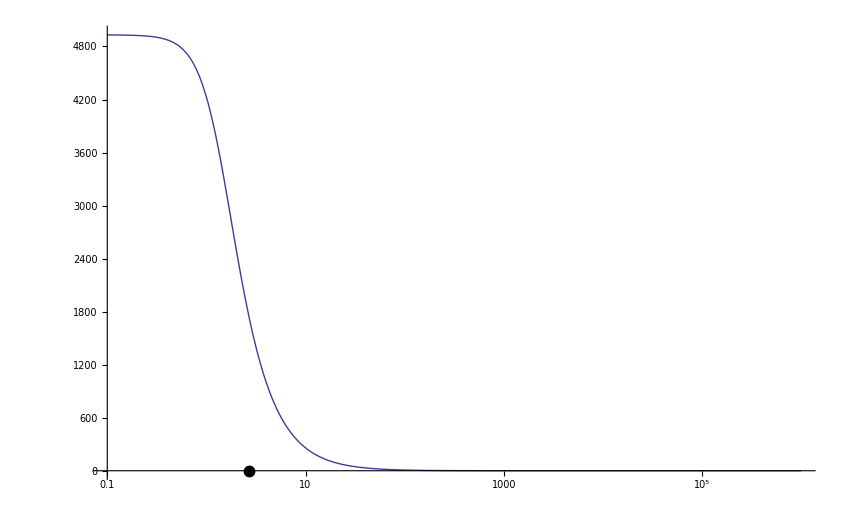

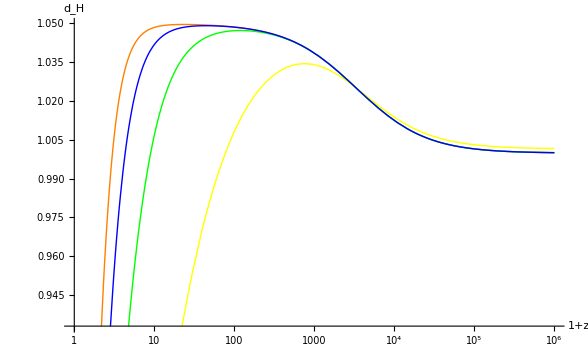

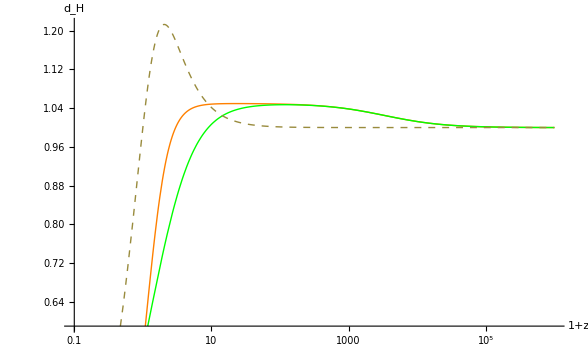

Plot growth factors in terms of 1+z

NIntegrate::nlim: x = 1/mn is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

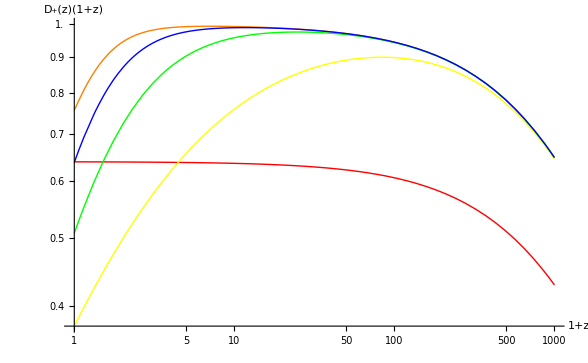

NIntegrate::nlim: x = 1/mn is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

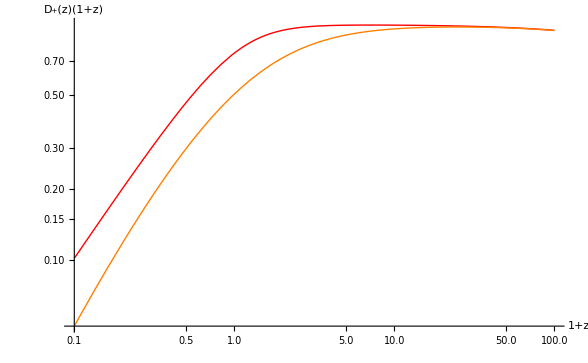

```mathematica
(*********************************************)
Print[Style["Parameters",Orange]]
(*********************************************)
Subscript[w, 1]=-1;
Subscript[w, 2]=-0.25;
Subscript[w, 3]=-0.5;
Subscript[w, 4]=-0.75;
Subscript[Ω, DE0]=0.734;
Subscript[Ω, k0]=0;
Subscript[Ω, m0]=0.1334/(0.71^2);
Subscript[Ω, r0]=8.09*10^-5;
h=0.71;
Subscript[H, 0]=(100 h)/300000;
Subscript[Ω, m0,s]=0.18670964881551225;Subscript[Ω, r0,s]=0.0000517586535727675;
(*********************************************)
Print[Style["Intial conditions for Hubble constant, normalized at equality",Orange]]
(*********************************************)
aeq=Subscript[Ω, r0]/Subscript[Ω, m0]
HL0=Subscript[H, 0];
Hs0=1.25 HL0
(*Hs0=(HL0 √(Subscript[Ω, m0] aeq^-3+Subscript[Ω, r0] aeq^-4+Subscript[Ω, DE0] aeq^(-3(1+Subscript[w, 1]))))/(√(Subscript[Ω, m0,s] aes^-3+Subscript[Ω, r0,s] aes^-4))*)
H20=(HL0 √(Subscript[Ω, m0] aeq^-3+Subscript[Ω, r0] aeq^-4+Subscript[Ω, DE0] aeq^(-3(1+Subscript[w, 1]))))/(√(Subscript[Ω, m0] aeq^-3+Subscript[Ω, r0] aeq^-4+Subscript[Ω, DE0] aeq^(-3(1+Subscript[w, 2]))))
H30=(HL0 √(Subscript[Ω, m0] aeq^-3+Subscript[Ω, r0] aeq^-4+Subscript[Ω, DE0] aeq^(-3(1+Subscript[w, 1]))))/(√(Subscript[Ω, m0] aeq^-3+Subscript[Ω, r0] aeq^-4+Subscript[Ω, DE0] aeq^(-3(1+Subscript[w, 3]))))
H40=(HL0 √(Subscript[Ω, m0] aeq^-3+Subscript[Ω, r0] aeq^-4+Subscript[Ω, DE0] aeq^(-3(1+Subscript[w, 1]))))/(√(Subscript[Ω, m0] aeq^-3+Subscript[Ω, r0] aeq^-4+Subscript[Ω, DE0] aeq^(-3(1+Subscript[w, 4]))))
(*********************************************)
Print[Style["Define Hubble functions",Orange]]
(*********************************************)
Subscript[H, s][a_]:=Hs0  √(Subscript[Ω, m0,s] a^-3+Subscript[Ω, r0,s] a^-4)
Subscript[H, L][a_]:=HL0  √(Subscript[Ω, m0] a^-3+Subscript[Ω, r0] a^-4+Subscript[Ω, DE0] a^(-3(1+Subscript[w, 1])))
Subscript[H, 2][a_]:=H20 √(Subscript[Ω, m0] a^-3+Subscript[Ω, r0] a^-4+Subscript[Ω, DE0] a^(-3(1+Subscript[w, 2])))
Subscript[H, 3][a_]:=H30 √(Subscript[Ω, m0] a^-3+Subscript[Ω, r0] a^-4+Subscript[Ω, DE0] a^(-3(1+Subscript[w, 3])))
Subscript[H, 4][a_]:=H40 √(Subscript[Ω, m0] a^-3+Subscript[Ω, r0] a^-4+Subscript[Ω, DE0] a^(-3(1+Subscript[w, 4])))
(*********************************************)
Print[Style["Hubble distances",Orange]]
(*********************************************)
Subscript[d, H,L][a]=1/(Subscript[H, L][a]);Subscript[d, H,2][a]=1/(Subscript[H, 2][a]);Subscript[d, H,3][a]=1/(Subscript[H, 3][a]);Subscript[d, H,4][a]=1/(Subscript[H, 4][a]);
(*********************************************)
Print[Style["Define k of a",Orange]]
(*********************************************)
kL[a_]=Subscript[H, L][a];Subscript[k, s][a_]=Subscript[H, s][a];Subscript[kDE, 2][a_]=Subscript[H, 2][a];Subscript[kDE, 3][a_]=Subscript[H, 3][a];Subscript[kDE, 4][a_]=Subscript[H, 4][a];
(*ss[k_]:=NSolve[k==Subscript[H, 1][Subscript[a, 1]]&&Subscript[a, 1]>0,Subscript[a, 1]]//FullSimplify
Solve[k==Subscript[H, 2][Subscript[a, 2]],Subscript[a, 2]];*)
(*********************************************)
Print[Style["Define growth factors",Orange]]
(*********************************************)
Growths[a_]:= 5/2 Subscript[Ω, m0,s] (Subscript[H, s][a])/Subscript[H, 0]  NIntegrate[1/(x^3((Subscript[H, s][x])/Subscript[H, 0])^3),{x,0,a}];
GrowthL[a_]:= 5/2 Subscript[Ω, m0] (Subscript[H, L][a])/Subscript[H, 0]  NIntegrate[1/(x^3((Subscript[H, L][x])/Subscript[H, 0])^3),{x,0,a}];
Subscript[GrowthDE, 2][a_]:=5/2 Subscript[Ω, m0] (Subscript[H, 2][a])/Subscript[H, 0]  NIntegrate[1/(x^3((Subscript[H, 2][x])/Subscript[H, 0])^3),{x,0,a}];
Subscript[GrowthDE, 3][a_]:=5/2 Subscript[Ω, m0] (Subscript[H, 3][a])/Subscript[H, 0]  NIntegrate[1/(x^3((Subscript[H, 3][x])/Subscript[H, 0])^3),{x,0,a}];
Subscript[GrowthDE, 4][a_]:=5/2 Subscript[Ω, m0] (Subscript[H, 4][a])/Subscript[H, 0]  NIntegrate[1/(x^3((Subscript[H, 4][x])/Subscript[H, 0])^3),{x,0,a}];
(*********************************************)
Print[Style["Plot k of a",Orange]]
(*********************************************)
LogPlot[{Subscript[k, s][a],kL[a],Subscript[kDE, 2][a],Subscript[kDE, 3][a],Subscript[kDE, 4][a]},{a,10^-3,1},PlotStyle->{Red,Orange,Yellow,Green,Blue}]
(*********************************************)
Print[Style["Plot growth factors of a for LCDM",Orange]]
(*********************************************)
ParametricPlot[{Log[kL[a]],Log[GrowthL[1]/GrowthL[a]]},{a,10^-3,1},PlotRange->Full,AxesOrigin-> {-9,0},PlotStyle->{Orange}]
(*********************************************)
Print[Style["Plot growth factors of a for all models",Orange]]
(*********************************************)
Plot[{Growths[a],GrowthL[a],Subscript[GrowthDE, 2][a],Subscript[GrowthDE, 3][a],Subscript[GrowthDE, 4][a]},{a,0,1},PlotStyle->{Red,Orange,Yellow,Green,Blue},AxesLabel-> {a,"D_+(a)"}];
LogLogPlot[{Growths[a],GrowthL[a],Subscript[GrowthDE, 2][a],Subscript[GrowthDE, 3][a],Subscript[GrowthDE, 4][a]},{a,10^-4,1},PlotStyle->{Red,Orange,Yellow,Green,Blue},AxesLabel-> {a,"D_+(a)"}]
(*********************************************)
Print[Style["Tranform growth factors / Hubble distances of a to those of 1+z",Orange]]
(*********************************************)
GS[mn_]:=Growths[1/mn];GL[mn_]:=GrowthL[1/mn];GDE2[mn_]:=Subscript[GrowthDE, 2][1/mn];GDE3[mn_]:=Subscript[GrowthDE, 3][1/mn];GDE4[mn_]:=Subscript[GrowthDE, 4][1/mn];
Lambdas[mn_]=1/(Subscript[H, s][1/mn]);LambdaL[mn_]=1/(Subscript[H, L][1/mn]);Lambda2[mn_]=1/(Subscript[H, 2][1/mn]);Lambda3[mn_]=1/(Subscript[H, 3][1/mn]);Lambda4[mn_]=1/(Subscript[H, 4][1/mn]);
(*********************************************)
Print[Style["Plot Hubble distances",Orange]]
(*********************************************)
LogLinearPlot[LambdaL[mn],{mn,0.1,10^6},Epilog->{PointSize[0.01],Point[{1,0}]}]
LogLinearPlot[{LambdaL[mn]/Lambdas[mn],Lambda2[mn]/Lambdas[mn],Lambda3[mn]/Lambdas[mn],Lambda4[mn]/Lambdas[mn]},{mn,1,10^6},PlotStyle->{Orange,Yellow,Green,Blue},AxesLabel->{"1+z","d_H"}]
LogLinearPlot[{LambdaL[mn]/Lambdas[mn],Lambda3[mn]/Lambdas[mn],LambdaL[mn]/Lambda3[mn]},{mn,0.1,10^6},PlotStyle->{Orange,Green,Dashed},AxesLabel->{"1+z","d_H"}]
(*********************************************)
Print[Style["Plot growth factors in terms of 1+z",Orange]]
(*********************************************)
LogLogPlot[{(mn)GS[mn],(mn)GL[mn],(mn)GDE2[mn],(mn)GDE3[mn],(mn)GDE4[mn]},{mn,1,1000},PlotStyle->{Red,Orange,Yellow,Green,Blue},AxesLabel-> {"1+z","D_+(z)(1+z)"}]
LogLogPlot[{(mn)GL[mn],(mn)GDE3[mn]},{mn,0.1,100},PlotStyle->{Red,Orange,Green},AxesLabel-> {"1+z","D_+(z)(1+z)"}]
(*LogLogPlot[{1,GL[mn]/GS[mn],GDE2[mn]/GS[mn],GDE3[mn]/GS[mn],GDE4[mn]/GS[mn]},{mn,0.1,100},AxesLabel-> {"1+z","D_+(z)(1+z)"}]*)
```

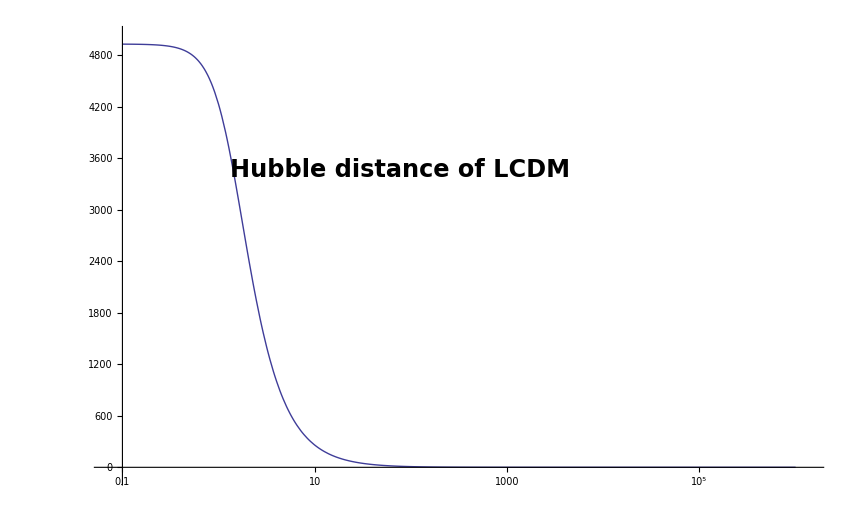

-Graphics-

-Graphics-

Plot growth factors in terms of 1+z

NIntegrate::nlim: x = 1/mn is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

-Graphics-

NIntegrate::nlim: x = 1/mn is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

-Graphics-